# Determination of α, β by fitting σ_R to ϵ at Q^2= 4.0 (GeV)^2

R^2/τ =A

2/R= B

2R/τ= X

R/τ= L

G_M^2 = G

σ_R = (G_M)^2 [1 + ϵ A + (B + ϵ X)[α1 (ϵ - 1) + α2 (ϵ^2 - 1)] + [B {1 -( 2 R ϵ/(1 + ϵ))} + 2 ϵ (1 + D)] [β1 (ϵ - 1) + β2 (ϵ^2 - 1)] ]

## Qattan

```mathematica
epsdata={0.473,0.593,0.694,0.19,0.946}; 
sigmaRdata={0.00546005,0.005097251,0.00520612,0.005117267,0.005282687};
data=Transpose[{epsdata,sigmaRdata}]
A=0.031469307
B=10.575216
X=0.332794715
L=0.166397358
G=0.009476956
R=0.189121433

sigmaR=G*(1+(eps*A) +((B+(eps*X))*(alpha1*(eps-1)+alpha2*(eps^2-1)))+(B*(1-((eps*2*R)/(1+eps)))+ 2*eps*(1+L))*(beta1*(eps-1)+beta2*(eps^2-1)))
FindFit[data, {sigmaR},{alpha1,alpha2,beta1,beta2},eps]
```

{{0.473,0.00546005},{0.593,0.00509725},{0.694,0.00520612},{0.19,0.00511727},{0.946,0.00528269}}

0.0314693

10.5752

0.332795

0.166397

0.00947696

0.189121

0.00947696 (1+0.0314693 eps+(10.5752+0.332795 eps) (alpha1 (-1+eps)+alpha2 (-1+eps^2))+(beta1 (-1+eps)+beta2 (-1+eps^2)) (2.33279 eps+10.5752 (1-(0.378243 eps)/(1+eps))))

{alpha1→71.4024,alpha2→-50.5775,beta1→-73.3511,beta2→52.0266}

## Y_E and Y_ 3 Determination with Plot

### α values :

```mathematica
alpha1=71.40241870422562
alpha2=-50.57746268433169
alpha0=-(alpha1+alpha2)
```

71.4024

-50.5775

-20.825

### β values :

```mathematica
beta1=-73.351104475958
beta2=52.02662257423083
beta0=-(beta1+beta2)
```

-73.3511

52.0266

21.3245

### Y_E , Y_ 3 & Y_M :

-20.825+71.4024 eps-50.5775 eps^2

21.3245-73.3511 eps+52.0266 eps^2

5.28761 (-20.825+71.4024 eps-50.5775 eps^2+(21.3245-73.3511 eps+52.0266 eps^2) (1-(0.378243 eps)/(1+eps)))

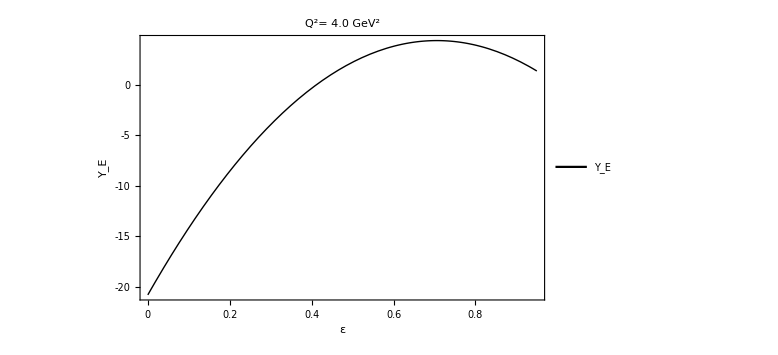

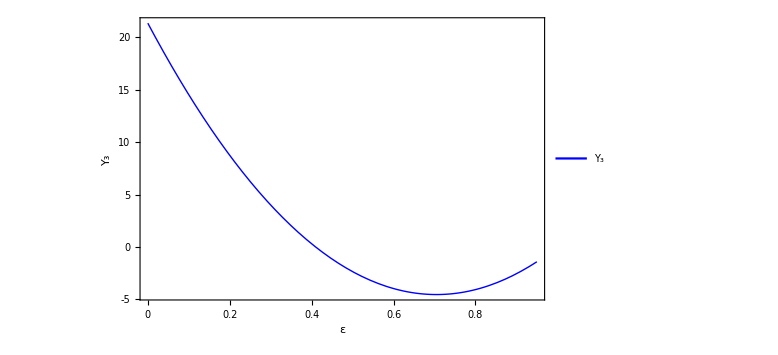

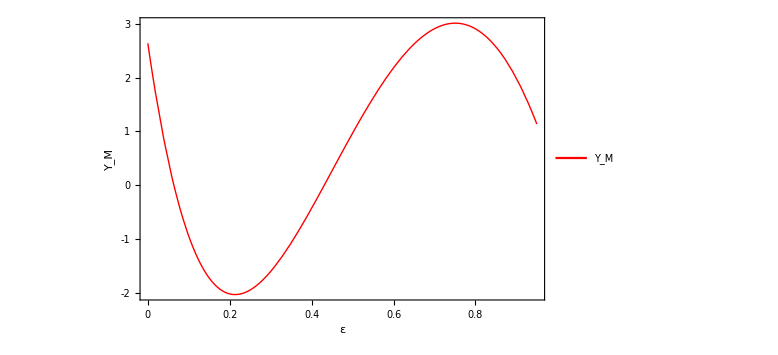

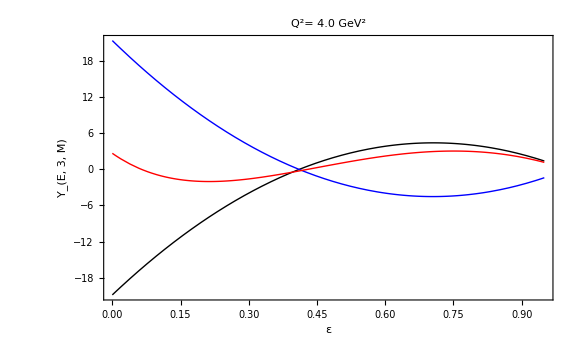

```mathematica
YE=-20.824956019893932+(71.40241870422562*eps)+(-50.57746268433169*eps^2)
Y3=21.324481901727168+(-73.351104475958*eps)+(52.02662257423083*eps^2)
YM=(YE+(1-R*(2*eps/(1+eps)))*Y3)/R
YEplot=Plot[YE, {eps,0,0.95},PlotStyle->{Black,Thick},FrameLabel->{Style["ε",Bold,16],Style["Y_E",Bold,16]},PlotLegends-> Placed[LineLegend[{"Y_E"},LabelStyle->Directive[22]],{0.92,0.8}], Frame-> True,FrameTicks->All,PlotLabel->Style["Q^2= 4.0 GeV^2",Bold,24], ImageSize-> Large]
Y3plot=Plot[Y3, {eps,0,0.95},PlotStyle->{Blue,Thick},FrameLabel->{Style["ε",Bold,18],Style["Y_3",Bold,18]},PlotLegends-> Placed[LineLegend[{"Y_3"},LabelStyle->Directive[22]],{0.92,0.8}],Frame-> True,FrameTicks->All,ImageSize-> Large]
YMplot=Plot[YM, {eps,0,0.95},PlotStyle->{Red, Thick},FrameLabel->{Style["ε",Bold,18],Style["Y_M",Bold,18]},PlotLegends-> Placed[LineLegend[{"Y_M"},LabelStyle->Directive[22]],{0.92,0.8}],Frame-> True,FrameTicks->All,ImageSize-> Large]

Show[YEplot,Y3plot,YMplot, PlotRange->All,FrameLabel->{Style["ε",Bold,26],Style["Y_(E, 3, M)  ",Bold,24]},Frame-> True,FrameTicks->All,FrameTicksStyle-> Directive[Black,12],ImageSize-> Large]
```

## My Fit

```mathematica
Q2=4
fcmuR=1+(-0.11723721716472688)*Q2+(0.0025226146422440594)*(Q2)^2+(-0.0004347472619650877)*(Q2)^3
fcR=fcmuR/2.7972
```

4

0.543589

0.194333

```mathematica
epsdata={0.473,0.593,0.694,0.19,0.946}; 
sigmaRdata={0.00546005,0.005097251,0.00520612,0.005117267,0.005282687};
data=Transpose[{epsdata,sigmaRdata}]
Afc=0.033399394
Bfc=10.26510838
Xfc=0.34285
Lfc=0.17142
Gfc=0.009459255
Rfc=0.19433331218762756

sigmaRfc=Gfc*(1+(eps*Afc) +((Bfc+(eps*Xfc))*(alpha1fc*(eps-1)+alpha2fc*(eps^2-1)))+(Bfc*(1-((eps*2*Rfc)/(1+eps)))+ 2*eps*(1+Lfc))*(beta1fc*(eps-1)+beta2fc*(eps^2-1)))
FindFit[data, {sigmaRfc},{alpha1fc,alpha2fc,beta1fc,beta2fc},eps]
```

{{0.473,0.00546005},{0.593,0.00509725},{0.694,0.00520612},{0.19,0.00511727},{0.946,0.00528269}}

0.0333994

10.2651

0.34285

0.17142

0.00945926

0.194333

0.00945926 (1+0.0333994 eps+(10.2651+0.34285 eps) (alpha1fc (-1+eps)+alpha2fc (-1+eps^2))+(beta1fc (-1+eps)+beta2fc (-1+eps^2)) (2.34284 eps+10.2651 (1-(0.388667 eps)/(1+eps))))

{alpha1fc→71.6831,alpha2fc→-50.6331,beta1fc→-73.678,beta2fc→52.1123}

```mathematica
{alpha1fc,alpha2fc,beta1fc,beta2fc}/.{alpha1fc->71.68310380323817,alpha2fc->-50.633146512777245,beta1fc->-73.67797897003716,beta2fc->52.11226000998139}
```

{71.6831,-50.6331,-73.678,52.1123}

```mathematica
alpha1fc=71.68310380323817
alpha2fc=-50.633146512777245
alpha0fc=-(alpha1fc+alpha2fc)
beta1fc=-73.67797897003716
beta2fc=52.11226000998139
beta0fc=-(beta1fc+beta2fc)
```

71.6831

-50.6331

-21.05

-73.678

52.1123

21.5657

```mathematica
YEfc=alpha0fc+(alpha1fc*eps)+(alpha2fc*eps^2)
Y3fc=beta0fc+(beta1fc*eps)+(beta2fc*eps^2)
YMfc=(YEfc+(1-Rfc*(2*eps/(1+eps)))*Y3fc)/Rfc
```

-21.05+71.6831 eps-50.6331 eps^2

21.5657-73.678 eps+52.1123 eps^2

5.1458 (-21.05+71.6831 eps-50.6331 eps^2+(21.5657-73.678 eps+52.1123 eps^2) (1-(0.388667 eps)/(1+eps)))

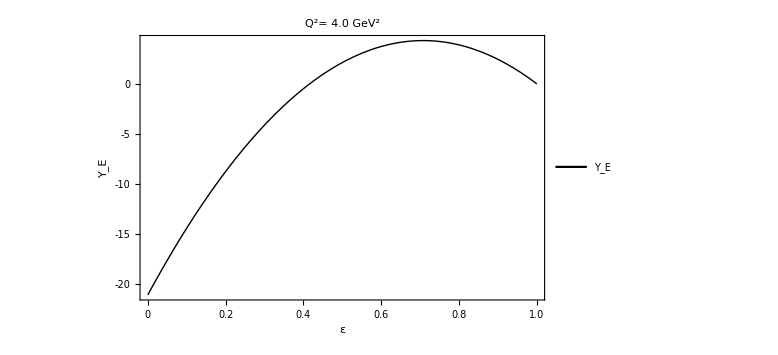

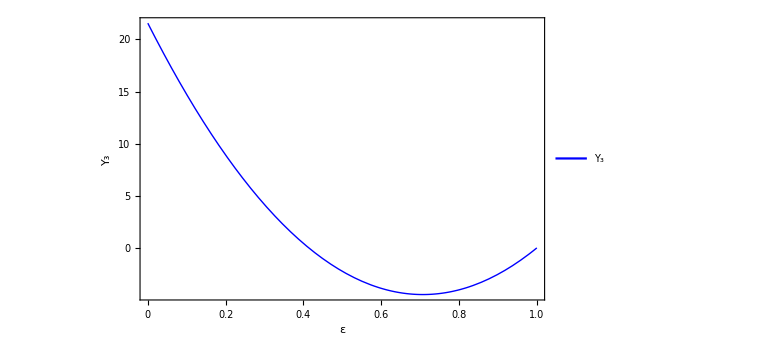

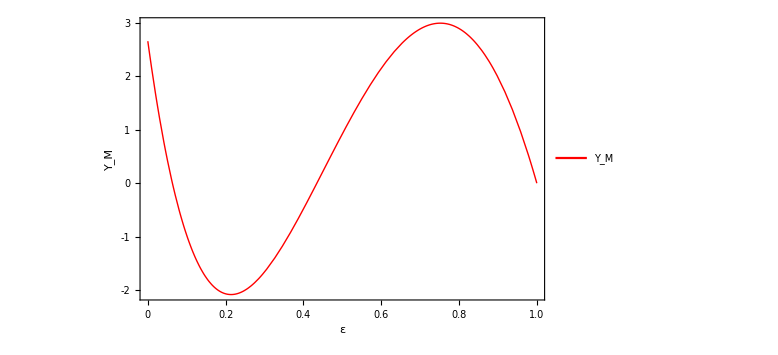

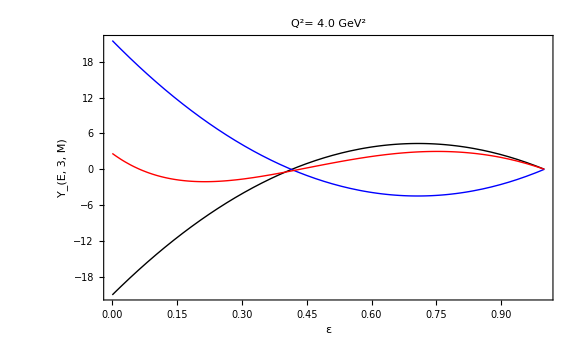

```mathematica
YEplotfc=Plot[YEfc, {eps,0,1},PlotStyle->{Black,Thick},FrameLabel->{Style["ε",Bold,16],Style["Y_E",Bold,16]},PlotLegends-> Placed[LineLegend[{"Y_E"},LabelStyle->Directive[22]],{0.9,0.8}], Frame-> True,FrameTicks->All,PlotLabel->Style["Q^2= 4.0 GeV^2",Bold,24], ImageSize-> Large]
Y3plotfc=Plot[Y3fc, {eps,0,1},PlotStyle->{Blue,Thick},FrameLabel->{Style["ε",Bold,18],Style["Y_3",Bold,18]},PlotLegends-> Placed[LineLegend[{"Y_3"},LabelStyle->Directive[22]],{0.9,0.8}],Frame-> True,FrameTicks->All,ImageSize-> Large]
YMplotfc=Plot[YMfc, {eps,0,1},PlotStyle->{Red, Thick},FrameLabel->{Style["ε",Bold,18],Style["Y_M",Bold,18]},PlotLegends-> Placed[LineLegend[{"Y_M"},LabelStyle->Directive[22]],{0.9,0.8}],Frame-> True,FrameTicks->All,ImageSize-> Large]

Show[YEplotfc,Y3plotfc,YMplotfc,PlotRange->All,FrameLabel->{Style["ε",Bold,26],Style["Y_(E, 3, M)  ",Bold,24]},Frame-> True,FrameTicks->All,FrameTicksStyle-> Directive[Black,14],ImageSize-> Large]
```